```mathematica
Clear["Global`*"];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΤΑΘΕΡΩΝ, 1 ΓΙΑ ΑΤΟΜΙΚΑ ΚΑΙ 2 ΓΙΑ ΠΥΡΗΝΙΚΑ ΣΥΣΤΗΜΑΤΑ *)
ic=1;
Which[ic==1,{c=26.247,ctime=6.586*10^(-16)},
         ic==2,{c=0.0482,ctime=6.586*10^(-22)}];
{v0=300, L=0.2, radius=Sqrt[c v0 L^2]};
```

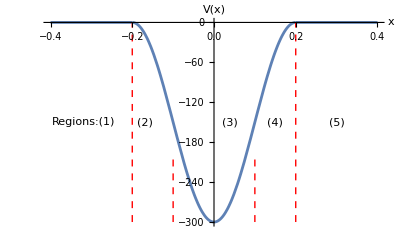

```mathematica
(*ΟΡΙΣΜΟΣ ΔΥΝΑΜΙΚΟΥ*)
V0=300;
L=0.2;

 v[x_]:=Which[  Abs[x]≤L, -(V0/2)*(1+Cos[Pi*x/L]),
                            Abs[x] >L, 0 ];
lineStyle={Thick,Red,Dashed};
line1=Line[{{-0.2,-300},{-0.2,0}}];
line2=Line[{{0.2,-300},{0.2,0}}];
line3=Line[{{0.1,-300},{0.1,-200}}];
line4=Line[{{-0.1,-300},{-0.1,-200}}];
 Plot[ v[x], {x, -2*L, 2*L}, PlotStyle ->AbsoluteThickness[2],
AxesStyle -> AbsoluteThickness[1], AxesLabel->{"x","V(x)"},
Epilog->{Text[StyleForm["Regions:(1)"], {-0.32, -150}] ,
                  Text[StyleForm[" (2)"], {-0.17, -150}],
                  Text[StyleForm[" (3)"], {0.04, -150}],
                  Text[StyleForm[" (4)"], {0.15, -150}],
                  Text[StyleForm[" (5)"], {0.3, -150}]  ,Directive[lineStyle],line1,line2,line3,line4   }   ]
```

```mathematica
(*ΕΥΡΕΣΗ ΙΔΙΟΤΙΜΩΝ*)
eta[x_]:=√(radius^2-x^2)/;x≤radius;
eta[x_]:=0/;x>radius;
etaEven[x_]:=x Tan[x];
etaOdd[x_]:=-x Cot[x];
```

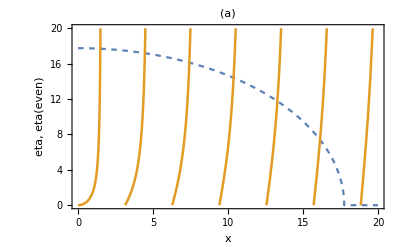

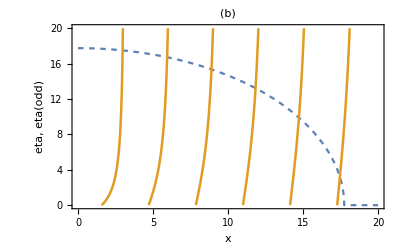

-Graphics-

```mathematica
(* PLOT ΓΙΑ ΑΡΤΙΕΣ(a) ΚΑΙ ΠΕΡΙΤΤΕΣ(b) ΚΑΤΑΣΤΑΣΕΙΣ *)
eEvenState=Plot[{eta[x],etaEven[x]},{x,0,20},PlotRange->{{0,20},{0.,20}},Frame->True,PlotStyle->{{Dashing[{0.01}]},{Thickness[0.0045]}},FrameLabel->{"x","eta,  eta(even)"},PlotLabel->"(a)"]
eOddState=Plot[{eta[x],etaOdd[x]},{x,0,20},PlotRange->{{0,20},{0.,20}},Frame->True,PlotStyle->{{Dashing[{0.01}]},{Thickness[0.0045]}},FrameLabel->{"x","eta,  eta(odd)"},PlotLabel->"(b)"]
```

```mathematica
(* ΕΥΡΕΣΗ ΣΗΜΕΙΩΝ ΤΟΜΗΣ ΓΙΑ ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΜΕ ΤΗ ΜΕΘΟΔΟ ΠΟΥ ΠΕΡΙΓΡΑΦΕΤΑΙ ΣΤΙΣ ΣΗΜΕΙΩΣΕΙΣ *)
(* ΑΝΑΛΟΓΑ ΜΕ ΤΟ ΜΕΓΕΘΟΣ ΤΗΣ ΓΡΑΦΙΚΗΣ ΠΑΡΑΣΤΑΣΗΣ ΑΛΛΑ ΚΑΙ ΤΗΣ ΑΝΑΛΥΣΗΣ ΤΗΣ ΟΘΟΝΗΣ ΣΑΣ ΜΠΟΡΕΙ ΝΑ ΟΔΗΓΗΘΕΙΤΕ ΣΕ ΔΙΑΦΟΡΕΤΙΚΑ ΑΠΟΤΕΛΕΣΜΑΤΑ *)
xieta={{1.46255,17.7328},{4.43098,17.2205},{7.4192,16.1958},{10.3481,14.4347},
{13.2769,11.745},{16.1266,7.42231}};
yieta={{3.0220713230966076,17.436052505488938},{5.964912289836075,16.703496088938895},{8.907753256575536,15.238383255838805},{11.850594223315001,13.132283558078825},{14.793435190054465,9.74421013146744},{17.509903774737047,3.059632830315252}};
(* ΥΠΟΛΟΓΙΣΜΟΣ ΤΩΝ 6 ΠΡΩΤΩΝ ΚΑΤΑΣΤΑΣΕΩΝ *)
EvenEnergyGraph=Table[-xieta[[i,2]]^2/(L^2 c),{i,1,6}];
Print["EvenEnergyGraph=",EvenEnergyGraph]
OddEnergyGraph=Table[-yieta[[i,2]]^2/(L^2 c),{i,1,6}];
Print["OddEnergyGraph=",OddEnergyGraph]
```

EvenEnergyGraph={-299.513,-282.457,-249.842,-198.461,-131.391,-52.4733}

OddEnergyGraph={-289.572,-265.751,-221.176,-164.263,-90.4386,-8.91659}

```mathematica
(* ΧΡΗΣΗ ΤΗΣ Findroot ΓΙΑ ΜΕΓΑΛΥΤΕΡΗ ΑΚΡΙΒΕΙΑ ΚΑΙ ΕΛΕΓΧΟΣ ΑΝ ΟΙ ΡΙΖΕΣ ΙΚΑΝΟΠΟΙΟΥΝ ΤΗΝ ΕΞΙΣΩΣΗ *)
EvenEnergy=Table[Null,{20}];
Do[{estart=EvenEnergyGraph[[i]],en=FindRoot[√(c (e+V0)) Sin[√(c (e+V0)) L]==√(-c e) Cos[√(c (e+V0)) L],{e,estart}],
EvenEnergy[[i]]=e/.en,ex=EvenEnergy[[i]],
test=√(c (ex+V0)) Tan[√(c (ex+V0)) L]-√(-c ex),Print["EvenEnergy[",i,"]=",EvenEnergy[[i]],"   test[",i, "]=, ",test]},
{i,1,6}];

(*  ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
OddEnergy=Table[Null,{20}];
Do[{estart=OddEnergyGraph[[i]],en=FindRoot[-√(c (e+V0))* Cos[√(c (e+V0)) L]==√(-c e)* Sin[√(c (e+V0)) L],{e,estart}],
OddEnergy[[i]]=e/.en,ex=OddEnergy[[i]],
test=√(c (ex+V0)) Cot[√(c (ex+V0)) L]+√(-c ex),Print["OddEnergy[",i,"]=",OddEnergy[[i]],"   test[",i, "]=, ",test]},
{i,1,6}];
```

EvenEnergy[1]=-297.894   test[1]=, 8.3844×10^-13

EvenEnergy[2]=-281.067   test[2]=, -2.4869×10^-12

EvenEnergy[3]=-247.524   test[3]=, 1.13687×10^-13

EvenEnergy[4]=-197.544   test[4]=, 2.98428×10^-13

EvenEnergy[5]=-131.748   test[5]=, -4.9738×10^-14

EvenEnergy[6]=-51.9626   test[6]=, 2.27374×10^-13

OddEnergy[1]=-291.58   test[1]=, -1.9611×10^-12

OddEnergy[2]=-266.372   test[2]=, -6.6791×10^-13

OddEnergy[3]=-224.562   test[3]=, -1.27898×10^-13

OddEnergy[4]=-166.559   test[4]=, 9.9476×10^-14

OddEnergy[5]=-93.3642   test[5]=, 6.39488×10^-14

OddEnergy[6]=-9.6594   test[6]=, -7.10543×10^-14

```mathematica
(*ΙΔΙΑ ΤΑΞΗ ΜΕΓΕΘΟΥΣ ΜΕ ΤΟ ΟΡΘΟΓΩΝΙΟ ΦΡΕΑΡ ΔΙΑΦΟΡΕΤΙΚΕΣ ΤΙΜΕΣ*)
```